```mathematica
NIntegrate[Cos[Sqrt[x^2+y^2]],{x,-Pi/2,Pi/2},{y,-Pi/2,Pi/2}]
```

3.17617

```mathematica
NIntegrate[Cos[Sqrt[x^2+y^2]],{x,0,4Pi},{y,0,4Pi}]
```

4.32326

```mathematica
Plot3D[Sqrt[Cos[x^2+y^2]],{x,-Sqrt[Pi/2],Sqrt[Pi/2]},{y,-Sqrt[Pi/2],Sqrt[Pi/2]}]
```

-Graphics3D-

```mathematica
Integrate[√2/8Cos[x],{x,-Pi/4,0}]
```

1/8

```mathematica
%/(Pi/2)
```

(2 √2)/π

```mathematica
N[%]
```

0.900316

```mathematica
Integrate[Cos[x],{x,0,2Pi}]
```

0

6/π+Cos[θ]/2-(4 Cos[4 θ])/(5 π)-(4 Cos[8 θ])/(21 π)-(12 Cos[12 θ])/(143 π)-(4 Cos[16 θ])/(85 π)-(4 Cos[20 θ])/(133 π)+Sin[θ]/2

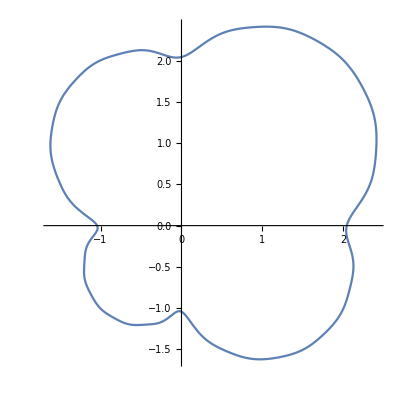

```mathematica
b00=3/π+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(5 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(21 π)+(2 Cos[10 θ])/(99 π)-(6 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(85 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(133 π)+Sin[θ]/2+3/π+Cos[θ]/2-(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(5 π)-(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(21 π)-(2 Cos[10 θ])/(99 π)-(6 Cos[12 θ])/(143 π)-(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(85 π)-(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(133 π)
PolarPlot[{b00},{θ,0,2Pi}]
```

Sin[θ]

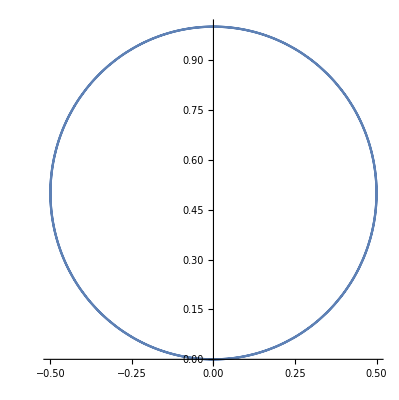

```mathematica
b00 =Cos[θ-Pi/2]
PolarPlot[{b00},{θ,0,2Pi}]
```

```mathematica
Clip[Cos[Pi/4],{0,1}]+Clip[Sin[Pi/4],{0,1}]
```

√2

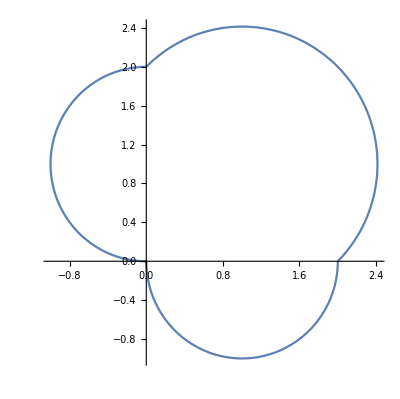

```mathematica
PolarPlot[{2*Clip[Cos[θ],{0,1}]+2*Clip[Sin[θ],{0,1}]},{θ,0,2Pi}]
```

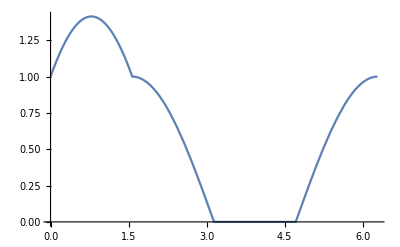

```mathematica
Plot[Clip[Cos[θ],{0,1}]+Clip[Sin[θ],{0,1}],{θ,0,2Pi}]
```

```mathematica
FourierSeries[Clip[Cos[θ],{0,1}]+2.7Clip[Sin[θ],{0,1}]+Clip[-Cos[θ],{0,1}],θ,20]
```

1.49606+(0.+0.675 ⅈ) ⅇ^(-ⅈ θ)-(0.+0.675 ⅈ) ⅇ^(ⅈ θ)-0.0742723 ⅇ^(-2 ⅈ θ)-0.0742723 ⅇ^(2 ⅈ θ)-0.0997371 ⅇ^(-4 ⅈ θ)-0.0997371 ⅇ^(4 ⅈ θ)-0.0063662 ⅇ^(-6 ⅈ θ)-0.0063662 ⅇ^(6 ⅈ θ)-0.0237469 ⅇ^(-8 ⅈ θ)-0.0237469 ⅇ^(8 ⅈ θ)-0.00225068 ⅇ^(-10 ⅈ θ)-0.00225068 ⅇ^(10 ⅈ θ)-0.0104619 ⅇ^(-12 ⅈ θ)-0.0104619 ⅇ^(12 ⅈ θ)-0.00114265 ⅇ^(-14 ⅈ θ)-0.00114265 ⅇ^(14 ⅈ θ)-0.00586689 ⅇ^(-16 ⅈ θ)-0.00586689 ⅇ^(16 ⅈ θ)-0.000689836 ⅇ^(-18 ⅈ θ)-0.000689836 ⅇ^(18 ⅈ θ)-0.00374951 ⅇ^(-20 ⅈ θ)-0.00374951 ⅇ^(20 ⅈ θ)

```mathematica
ExpToTrig[%22]
```

1.49606+(0.+0.675 ⅈ) (Cos[θ]-ⅈ Sin[θ])-(0.+0.675 ⅈ) (Cos[θ]+ⅈ Sin[θ])-0.0742723 (Cos[2 θ]-ⅈ Sin[2 θ])-0.0742723 (Cos[2 θ]+ⅈ Sin[2 θ])-0.0997371 (Cos[4 θ]-ⅈ Sin[4 θ])-0.0997371 (Cos[4 θ]+ⅈ Sin[4 θ])-0.0063662 (Cos[6 θ]-ⅈ Sin[6 θ])-0.0063662 (Cos[6 θ]+ⅈ Sin[6 θ])-0.0237469 (Cos[8 θ]-ⅈ Sin[8 θ])-0.0237469 (Cos[8 θ]+ⅈ Sin[8 θ])-0.00225068 (Cos[10 θ]-ⅈ Sin[10 θ])-0.00225068 (Cos[10 θ]+ⅈ Sin[10 θ])-0.0104619 (Cos[12 θ]-ⅈ Sin[12 θ])-0.0104619 (Cos[12 θ]+ⅈ Sin[12 θ])-0.00114265 (Cos[14 θ]-ⅈ Sin[14 θ])-0.00114265 (Cos[14 θ]+ⅈ Sin[14 θ])-0.00586689 (Cos[16 θ]-ⅈ Sin[16 θ])-0.00586689 (Cos[16 θ]+ⅈ Sin[16 θ])-0.000689836 (Cos[18 θ]-ⅈ Sin[18 θ])-0.000689836 (Cos[18 θ]+ⅈ Sin[18 θ])-0.00374951 (Cos[20 θ]-ⅈ Sin[20 θ])-0.00374951 (Cos[20 θ]+ⅈ Sin[20 θ])

```mathematica
ExpToTrig[%]
```

3/π+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(5 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(21 π)+(2 Cos[10 θ])/(99 π)-(6 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(85 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(133 π)+Sin[θ]/2

1.49606+(0.+0.675 ⅈ) (Cos[θ]-ⅈ Sin[θ])-(0.+0.675 ⅈ) (Cos[θ]+ⅈ Sin[θ])-0.0742723 (Cos[2 θ]-ⅈ Sin[2 θ])-0.0742723 (Cos[2 θ]+ⅈ Sin[2 θ])-0.0997371 (Cos[4 θ]-ⅈ Sin[4 θ])-0.0997371 (Cos[4 θ]+ⅈ Sin[4 θ])-0.0063662 (Cos[6 θ]-ⅈ Sin[6 θ])-0.0063662 (Cos[6 θ]+ⅈ Sin[6 θ])-0.0237469 (Cos[8 θ]-ⅈ Sin[8 θ])-0.0237469 (Cos[8 θ]+ⅈ Sin[8 θ])-0.00225068 (Cos[10 θ]-ⅈ Sin[10 θ])-0.00225068 (Cos[10 θ]+ⅈ Sin[10 θ])-0.0104619 (Cos[12 θ]-ⅈ Sin[12 θ])-0.0104619 (Cos[12 θ]+ⅈ Sin[12 θ])-0.00114265 (Cos[14 θ]-ⅈ Sin[14 θ])-0.00114265 (Cos[14 θ]+ⅈ Sin[14 θ])-0.00586689 (Cos[16 θ]-ⅈ Sin[16 θ])-0.00586689 (Cos[16 θ]+ⅈ Sin[16 θ])-0.000689836 (Cos[18 θ]-ⅈ Sin[18 θ])-0.000689836 (Cos[18 θ]+ⅈ Sin[18 θ])-0.00374951 (Cos[20 θ]-ⅈ Sin[20 θ])-0.00374951 (Cos[20 θ]+ⅈ Sin[20 θ])

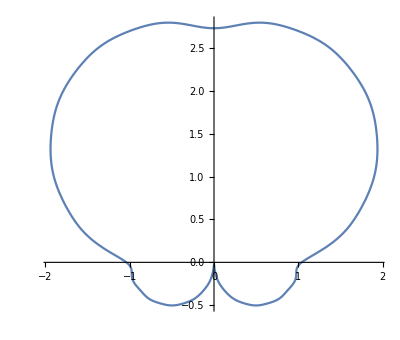

```mathematica
b00 =1.4960564650638164+(0.+0.675 ⅈ) (Cos[θ]-ⅈ Sin[θ])-(0.+0.675 ⅈ) (Cos[θ]+ⅈ Sin[θ])-0.07427230677621782 (Cos[2 θ]-ⅈ Sin[2 θ])-0.07427230677621782 (Cos[2 θ]+ⅈ Sin[2 θ])-0.0997370976709211 (Cos[4 θ]-ⅈ Sin[4 θ])-0.0997370976709211 (Cos[4 θ]+ⅈ Sin[4 θ])-0.006366197723675814 (Cos[6 θ]-ⅈ Sin[6 θ])-0.006366197723675814 (Cos[6 θ]+ⅈ Sin[6 θ])-0.023746928016885972 (Cos[8 θ]-ⅈ Sin[8 θ])-0.023746928016885972 (Cos[8 θ]+ⅈ Sin[8 θ])-0.002250675962915692 (Cos[10 θ]-ⅈ Sin[10 θ])-0.002250675962915692 (Cos[10 θ]+ⅈ Sin[10 θ])-0.010461933322124589 (Cos[12 θ]-ⅈ Sin[12 θ])-0.010461933322124589 (Cos[12 θ]+ⅈ Sin[12 θ])-0.0011426508734802743 (Cos[14 θ]-ⅈ Sin[14 θ])-0.0011426508734802743 (Cos[14 θ]+ⅈ Sin[14 θ])-0.005866888098289476 (Cos[16 θ]-ⅈ Sin[16 θ])-0.005866888098289476 (Cos[16 θ]+ⅈ Sin[16 θ])-0.000689835666652178 (Cos[18 θ]-ⅈ Sin[18 θ])-0.000689835666652178 (Cos[18 θ]+ⅈ Sin[18 θ])-0.003749514950034627 (Cos[20 θ]-ⅈ Sin[20 θ])-0.003749514950034627 (Cos[20 θ]+ⅈ Sin[20 θ])
PolarPlot[{b00},{θ,0,2Pi}]
```

3/π+Cos[θ]/2-(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(5 π)-(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(21 π)-(2 Cos[10 θ])/(99 π)-(6 Cos[12 θ])/(143 π)-(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(85 π)-(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(133 π)

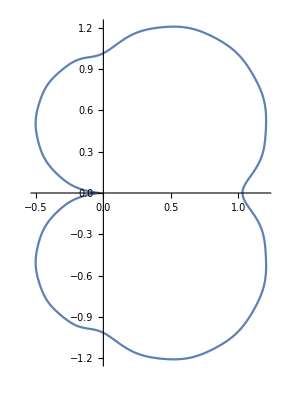

```mathematica
b00 =3/π+Cos[θ]/2-(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(5 π)-(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(21 π)-(2 Cos[10 θ])/(99 π)-(6 Cos[12 θ])/(143 π)-(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(85 π)-(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(133 π)
PolarPlot[{b00},{θ,0,2Pi}]
```

```mathematica
FourierSeries[Clip[Cos[θ],{0,1}]+Clip[Sin[θ],{0,1}]+2Clip[-Sin[θ],{0,1}],θ,20]
```

(1/4-ⅈ/4) ⅇ^(-ⅈ θ)+(1/4+ⅈ/4) ⅇ^(ⅈ θ)+4/π-(2 ⅇ^(-2 ⅈ θ))/(3 π)-(2 ⅇ^(2 ⅈ θ))/(3 π)-(4 ⅇ^(-4 ⅈ θ))/(15 π)-(4 ⅇ^(4 ⅈ θ))/(15 π)-(2 ⅇ^(-6 ⅈ θ))/(35 π)-(2 ⅇ^(6 ⅈ θ))/(35 π)-(4 ⅇ^(-8 ⅈ θ))/(63 π)-(4 ⅇ^(8 ⅈ θ))/(63 π)-(2 ⅇ^(-10 ⅈ θ))/(99 π)-(2 ⅇ^(10 ⅈ θ))/(99 π)-(4 ⅇ^(-12 ⅈ θ))/(143 π)-(4 ⅇ^(12 ⅈ θ))/(143 π)-(2 ⅇ^(-14 ⅈ θ))/(195 π)-(2 ⅇ^(14 ⅈ θ))/(195 π)-(4 ⅇ^(-16 ⅈ θ))/(255 π)-(4 ⅇ^(16 ⅈ θ))/(255 π)-(2 ⅇ^(-18 ⅈ θ))/(323 π)-(2 ⅇ^(18 ⅈ θ))/(323 π)-(4 ⅇ^(-20 ⅈ θ))/(399 π)-(4 ⅇ^(20 ⅈ θ))/(399 π)

```mathematica
ExpToTrig[%]
```

4/π+Cos[θ]/2-(4 Cos[2 θ])/(3 π)-(8 Cos[4 θ])/(15 π)-(4 Cos[6 θ])/(35 π)-(8 Cos[8 θ])/(63 π)-(4 Cos[10 θ])/(99 π)-(8 Cos[12 θ])/(143 π)-(4 Cos[14 θ])/(195 π)-(8 Cos[16 θ])/(255 π)-(4 Cos[18 θ])/(323 π)-(8 Cos[20 θ])/(399 π)-Sin[θ]/2

2/π+(4 Cos[2 θ])/(3 π)-(4 Cos[4 θ])/(15 π)+(4 Cos[6 θ])/(35 π)-(4 Cos[8 θ])/(63 π)+(4 Cos[10 θ])/(99 π)-(4 Cos[12 θ])/(143 π)+(4 Cos[14 θ])/(195 π)-(4 Cos[16 θ])/(255 π)+(4 Cos[18 θ])/(323 π)-(4 Cos[20 θ])/(399 π)

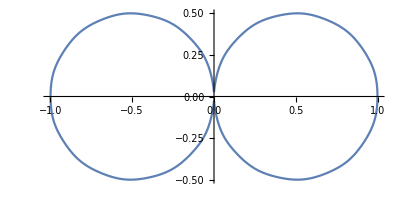

```mathematica
b00 =1/π-Cos[θ]/2+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)+(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)+1/π+Cos[θ]/2+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)+(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)
PolarPlot[{b00},{θ,0,2Pi}]
```

0.5 (Abs[Sin[π/4-θ]]+Cos[π/4-θ])

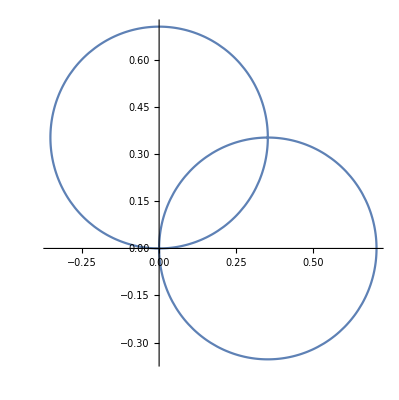

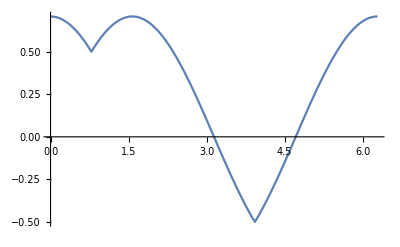

```mathematica
b00 =0.5(Cos[1θ-Pi/4]+1Abs[Sin[1θ-Pi/4]])
PolarPlot[{b00},{θ,0,2Pi}]
Plot[{b00},{θ,0,2Pi}]
```

1/π+Cos[θ]/2+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)+(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)

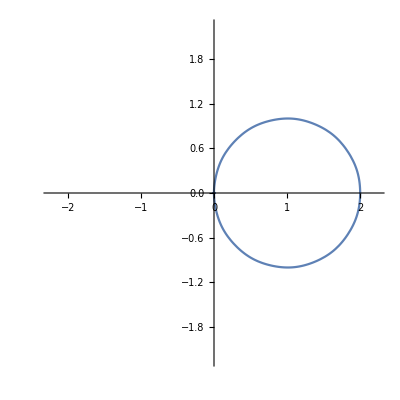

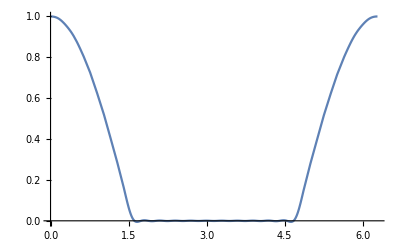

```mathematica
b00 =1/π+Cos[θ]/2+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)+(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)
PolarPlot[{2*b00},{θ,0,2Pi},PlotRange->All]
Plot[{b00},{θ,0,2Pi}]
```

```mathematica
FourierSeries[Clip[Cos[θ],{0,1}],θ,20]
```

ⅇ^(-ⅈ θ)/4+ⅇ^(ⅈ θ)/4+1/π+ⅇ^(-2 ⅈ θ)/(3 π)+ⅇ^(2 ⅈ θ)/(3 π)-ⅇ^(-4 ⅈ θ)/(15 π)-ⅇ^(4 ⅈ θ)/(15 π)+ⅇ^(-6 ⅈ θ)/(35 π)+ⅇ^(6 ⅈ θ)/(35 π)-ⅇ^(-8 ⅈ θ)/(63 π)-ⅇ^(8 ⅈ θ)/(63 π)+ⅇ^(-10 ⅈ θ)/(99 π)+ⅇ^(10 ⅈ θ)/(99 π)-ⅇ^(-12 ⅈ θ)/(143 π)-ⅇ^(12 ⅈ θ)/(143 π)+ⅇ^(-14 ⅈ θ)/(195 π)+ⅇ^(14 ⅈ θ)/(195 π)-ⅇ^(-16 ⅈ θ)/(255 π)-ⅇ^(16 ⅈ θ)/(255 π)+ⅇ^(-18 ⅈ θ)/(323 π)+ⅇ^(18 ⅈ θ)/(323 π)-ⅇ^(-20 ⅈ θ)/(399 π)-ⅇ^(20 ⅈ θ)/(399 π)

```mathematica
ExpToTrig[%114]
```

1/π+Cos[θ]/2+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)+(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)

```mathematica
ExpToTrig[%111]
```

```mathematica
ExpToTrig[%61]
```

1/π-(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)-(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)-(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)-(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)-(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)+Sin[θ]/2

```mathematica
ExpToTrig[%57]
```

1/π+Cos[θ]/2+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)+(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)

2/π+Cos[θ]/2-(4 Cos[4 θ])/(15 π)-(4 Cos[8 θ])/(63 π)-(4 Cos[12 θ])/(143 π)-(4 Cos[16 θ])/(255 π)-(4 Cos[20 θ])/(399 π)+Sin[θ]/2

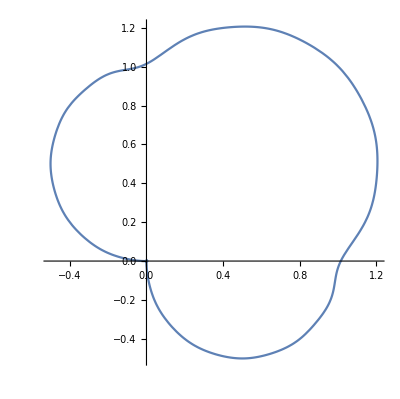

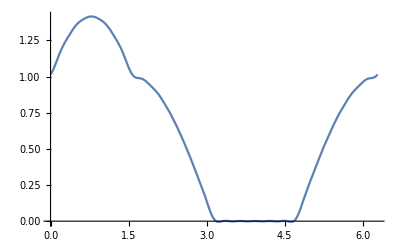

```mathematica
b00 =1/π+Cos[θ]/2+(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)+(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)+(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)+(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)+(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)+1/π-(2 Cos[2 θ])/(3 π)-(2 Cos[4 θ])/(15 π)-(2 Cos[6 θ])/(35 π)-(2 Cos[8 θ])/(63 π)-(2 Cos[10 θ])/(99 π)-(2 Cos[12 θ])/(143 π)-(2 Cos[14 θ])/(195 π)-(2 Cos[16 θ])/(255 π)-(2 Cos[18 θ])/(323 π)-(2 Cos[20 θ])/(399 π)+Sin[θ]/2
PolarPlot[{b00},{θ,0,2Pi}]
Plot[{b00},{θ,0,2Pi}]
```

2 (0.636+0.707 Cos[θ]+0.707 Sin[θ]-0.42 Sin[2 θ])

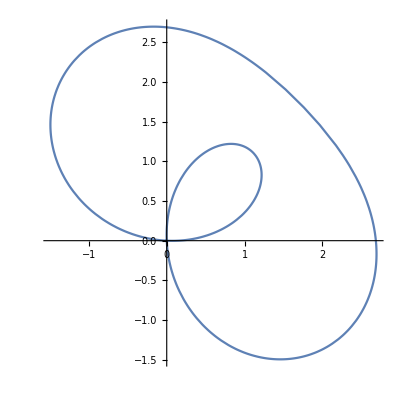

```mathematica
b00 =2*(0.636+0.707Cos[1θ]+0.707Sin[1θ]-0.42Sin[2θ])
PolarPlot[{b00},{θ,0,2Pi}]
```

```mathematica
0.636+0.707Cos[-2Pi/4]+0.707Sin[-2Pi/4]-0.42Sin[2*-2Pi/4]
```

-0.071

Abs[Sin[π/4-θ]]-Cos[π/4-θ]

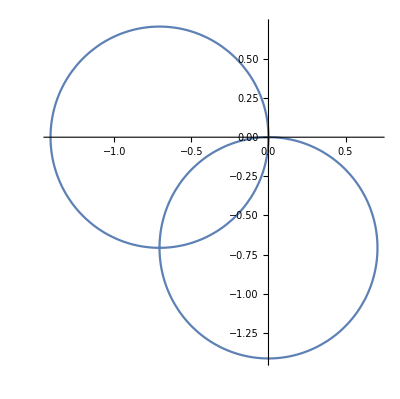

```mathematica
b00 =1Cos[1θ-5Pi/4]+1Abs[Sin[1θ-5Pi/4]]
PolarPlot[{b00},{θ,0,2Pi}]
```

0.636-0.707 Cos[θ]-0.707 Sin[θ]-0.42 Sin[2 θ]

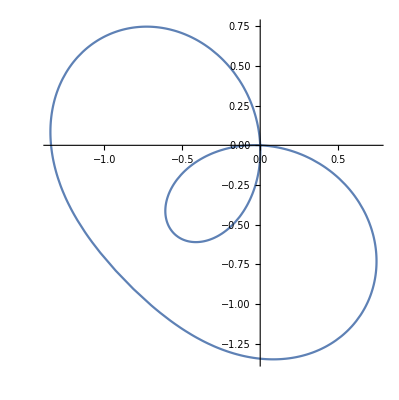

```mathematica
b00 =0.636-0.707Cos[1θ]-0.707Sin[1θ]-0.42Sin[2θ]
PolarPlot[{b00},{θ,0,2Pi}]
```

Abs[Sin[θ]]+Cos[2 θ]

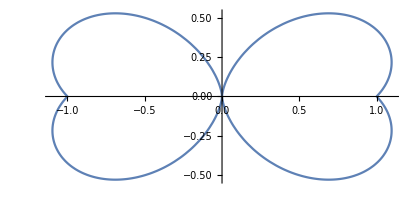

```mathematica
b00 =1Abs[Sin[1θ]]+Cos[2θ]
PolarPlot[{b00},{θ,0,2Pi}]
```

```mathematica
π*(1/2)^2
Sqrt[π*(1/2)^2]
```

π/4

(√π)/2

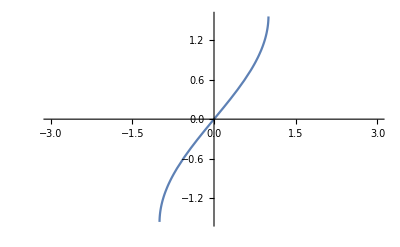

```mathematica
Plot[ArcSin[x],{x,-3,3}]
```

```mathematica
FourierSeries[t,t,3]
```

ⅈ ⅇ^(-ⅈ t)-ⅈ ⅇ^(ⅈ t)-1/2 ⅈ ⅇ^(-2 ⅈ t)+1/2 ⅈ ⅇ^(2 ⅈ t)+1/3 ⅈ ⅇ^(-3 ⅈ t)-1/3 ⅈ ⅇ^(3 ⅈ t)

```mathematica
ExpToTrig[ⅈ ⅇ^(-ⅈ t)-ⅈ ⅇ^(ⅈ t)-1/2 ⅈ ⅇ^(-2 ⅈ t)+1/2 ⅈ ⅇ^(2 ⅈ t)+1/3 ⅈ ⅇ^(-3 ⅈ t)-1/3 ⅈ ⅇ^(3 ⅈ t)]
```

2 Sin[t]-Sin[2 t]+2/3 Sin[3 t]

```mathematica
∫_0^(2Pi) Clip[-Cos[θ],{0,1}]*Clip[Cos[θ],{0,1}]ⅆθ
```

0

```mathematica
∫_0^(2Pi) Clip[-Cos[θ],{0,1}]*Clip[Cos[θ],{0,1}]ⅆθ
```